```mathematica
fLogistic[t_,r_,k_,N0_]:=k /(1+((k-N0)/N0) Exp[-r t])
```

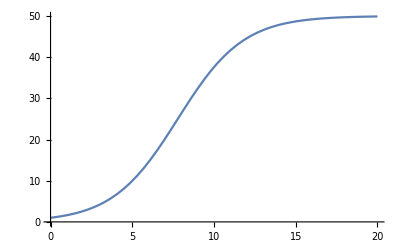

```mathematica
Plot[fLogistic[t,0.5,50,1],{t,0,20}]
```

```mathematica
lData = Table[{t,fLogistic[t,0.5,50,1]+RandomVariate[NormalDistribution[0,5],{1}][[1]]},{t,0,20,2}]
```

{{0,0.669078},{2,3.20348},{4,8.86817},{6,13.8817},{8,18.5653},{10,42.6368},{12,40.9434},{14,40.254},{16,46.9597},{18,52.5767},{20,51.2119}}

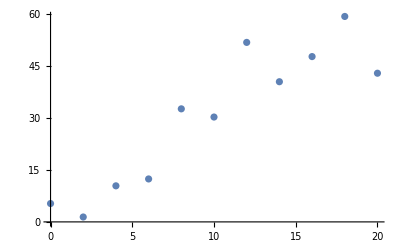

```mathematica
ListPlot[lData]
```

```mathematica
fNormalLikelihoodPoint[r_,k_,σ_,N0_,X_,t_]:=Likelihood[NormalDistribution[fLogistic[t,r,k,N0],σ],{X}]
```

```mathematica
NIntegrate[fNormalLikelihoodPoint[r,k,σ,1,30,10],{r,0,2},{k,0,100},{σ,0,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19.579 and 0.000794823 for the integral and error estimates.

19.579

```mathematica
Integrate[fNormalLikelihoodPoint[r,k,σ,1,30,10],{r,0,2},{k,0,100},{σ,0,10}]
```

(∫_0^2 ∫_0^100 Gamma[0,((ⅇ^(10 r) (-30+k)-30 (-1+k))^2)/(200 (-1+ⅇ^(10 r)+k)^2)]ⅆkⅆr)/(2 √(2 π))

```mathematica
fNormalLikelihoodAll[r_,k_,σ_,N0_,X__,t__]:=Product[Likelihood[NormalDistribution[fLogistic[t[[i]],r,k,N0],σ],{X[[i]]}],{i,1,Length@X,1}]
```

```mathematica
fNormalLikelihoodAll[0.5,50,5,1,lData[[All,2]],lData[[All,1]]]
```

4.03113×10^-16

```mathematica
Integrate[fNormalLikelihoodAll[r,k,σ,1,lData[[All,2]],lData[[All,1]]],{r,0,2},{k,0,100},{σ,0,10}]
```

$Aborted

```mathematica
Assuming[{n>0,c>0},Integrate[(1/(a^(n/2)))Exp[-b/(a^2)],{a,0,c}]]
```

ConditionalExpression[1/2 b^(1/2-n/4) Gamma[1/4 (-2+n),b/c^2],(Re[b]≥0&&n<4)||Re[b]>0]

## Normal distribution

```mathematica
lData=RandomVariate[NormalDistribution[5,1],{10}];
```

```mathematica
fLimitedLikelihood[μ_,X__,sigmaRange_]:=Block[{n=Length@X,b=Total[(X-μ)^2]},1/2 (1/b)^(1/4 (-2+n)) Gamma[1/4 (-2+n),b/sigmaRange^2]]
```

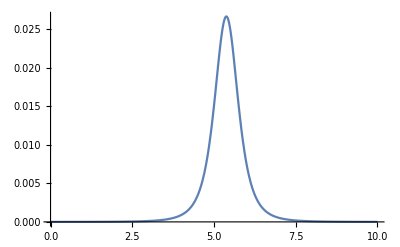

```mathematica
Plot[fLimitedLikelihood[μ,lData,10],{μ,0,10},PlotRange->Full]
```

## Logistic limited likelihood

```mathematica
fLimitedLikelihoodLogistic[r_,k_,N0_,y__,t__,sigmaRange_]:=Block[{SSE = Total[Table[(y[[i]]-fLogistic[t[[i]],r,k,N0])^2,{i,1,Length@y,1}]],n=Length@y},1/2 SSE^(1/2-n/4) Gamma[1/4 (-2+n),SSE/sigmaRange^2]]
```

```mathematica
lData = Table[{t,fLogistic[t,0.5,50,1]+RandomVariate[NormalDistribution[0,5],{1}][[1]]},{t,0,20,2}];
```

```mathematica
aInt=NIntegrate[fLimitedLikelihoodLogistic[r,k,1,lData[[All,2]],lData[[All,1]],10],{r,0,20},{k,0,1000}]
```

6.20615×10^-7

```mathematica
Assuming[{n>0,c>0,b>0},Integrate[(1/(a^(n/2)))Exp[-b/(a^2)] Exp[-1/(a^2)],{a,0,c}]]
```

1/2 (1+b)^(1/2-n/4) Gamma[1/4 (-2+n),(1+b)/c^2]

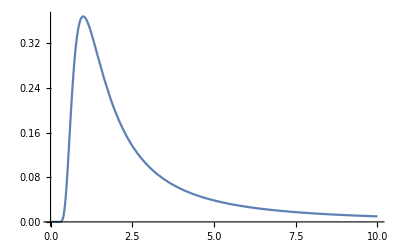

```mathematica
Plot[(1/a^2) Exp[-1/a^2],{a,0,10},PlotRange->Full]
```

```mathematica
NIntegrate[(1/a^2) Exp[-1/a^2],{a,0,∞}]
```

0.886227

### Work out posterior quantiles

```mathematica
aInt=NIntegrate[fLimitedLikelihoodLogistic[r,k,1,lData[[All,2]],lData[[All,1]],10],{r,0,20},{k,0,1000}]
```

6.20615×10^-7

```mathematica
kMean=NIntegrate[(1/aInt) k fLimitedLikelihoodLogistic[r,k,1,lData[[All,2]],lData[[All,1]],10],{r,0,20},{k,0,1000}]
rMean=NIntegrate[(1/aInt)r fLimitedLikelihoodLogistic[r,k,1,lData[[All,2]],lData[[All,1]],10],{r,0,20},{k,0,1000}]
```

43.4423

0.585731

```mathematica
kVar=NIntegrate[(1/aInt) (k-kMean)^2 fLimitedLikelihoodLogistic[r,k,1,lData[[All,2]],lData[[All,1]],10],{r,0,20},{k,0,1000}]
rVar=NIntegrate[(1/aInt) (r-rMean)^2 fLimitedLikelihoodLogistic[r,k,1,lData[[All,2]],lData[[All,1]],10],{r,0,20},{k,0,1000}]
```

1.26856

0.0033155

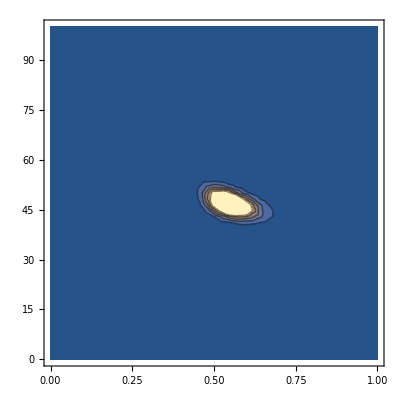

```mathematica
ContourPlot[fLimitedLikelihoodLogistic[r,k,1,lData[[All,2]],lData[[All,1]],10],{r,0,1},{k,0,100},PlotRange->Full]
```

```mathematica
N@Log@Integrate[x^2,{x,1,10}]
```

5.80814

```mathematica
N@Integrate[Log[x^2],{x,1,10}]
```

28.0517